# QNM Amplitude: Time and Frequency domain analysis

```mathematica
Quit[]
```

```mathematica
Clear["Global`*"]
<<MaTeX`
SetDirectory[NotebookDirectory[]];
$Assumptions={M>0}
DirName=NotebookDirectory[];
```

{M>0}

## Parameters

## Physical Parameters

### Wave equation Parameters

```mathematica
Mbh=rh/2;
λ=rh;
spin=2;
l=2;
```

### Bump Parameters

```mathematica
ModelName="BumpPT";
 ao= 115722/10000; (*120000/10000;*)
 ϵ=204/100000;
```

## Numerical Parameters

```mathematica
Prec=10*MachinePrecision;


Nz$dom0=75;
Nz$dom1=75;


Nz$QNMload$dom0=75;
Nz$QNMload$dom1=75;
```

### QNM Selection

```mathematica
N$QNM$max=8;
```

## Schwarzschild Spacetime

## Metric Function

```mathematica
a=1-rh/r;
b=a;
f=FullSimplify[Sqrt[a*b], Assumptions->{rh>0, r>rh}];
ζ$of$r=FullSimplify[Sqrt[a/b], Assumptions->{rh>0, r>rh}];
```

```mathematica
m=r/2*(1-b);

fAsymp=Normal@Series[f,{r,Infinity,1}]//Expand;
M$ADM=-Coefficient[fAsymp,r,-1]/2//FullSimplify;
SubsM={M->M$ADM}
```

{M→rh/2}

## Hyperboloidal Formulation

## Radial Compactfication

### Areal Radius

```mathematica
ρ1=0;(*rh/λ 1/(1-σ0)*)
ρ0=rh/λ-ρ1;

ρ[σ_]:=ρ0+ρ1*σ
β=ρ[σ]-σ*D[ρ[σ],σ]//FullSimplify;
```

### Radial Mapping

```mathematica
r$of$σ[σ_]:=λ ρ[σ]/σ;
dr$dσ=D[r$of$σ[σ],σ];

σ$of$r=σ/.Solve[r$of$σ[σ]==r,σ][[1]];
```

```mathematica
σh=σhrz/.Solve[r$of$σ[σhrz]==rh,σhrz][[1]];
```

### Metric function and deviation function in compact coordinate

```mathematica
F=Simplify[f/.r->r$of$σ[σ]];
ζ=Simplify[ζ$of$r/.r->r$of$σ[σ]];
```

#### Find Horizons

```mathematica
SubsσHrz=Solve[{F==0, σ>0},σ,Reals];
σHrz=σ/.SubsσHrz;
nHrz=Length@σHrz;
rHrz=r$of$σ[σHrz];
```

#### Representation as in eq. 2.13 - Event Horizon

```mathematica
root$rh=(1-rHrz/r)/.r->r$of$σ[σ]//FullSimplify;
Kh=Expand[F/root$rh]//FullSimplify;
```

## Dimensionless Tortoise Coordinate

### Differential Equation (eq. 2.11)

```mathematica
dx$dσ=FullSimplify[-β/(σ^2F)];
```

### Contribution from Infinity (eq. 4.7)

```mathematica
x$0=ρ0/σ-2M/λ Log[σ];
dx0$dσ=FullSimplify[D[x$0,σ]];
```

### Contribution from Event Horizon (eq. 4.5)

```mathematica
KBHHrz=Table[Limit[Kh[[i]],SubsσHrz[[i]]],{i,1,nHrz}];
x$BHHrz=Table[rHrz[[i]]/(λ*KBHHrz[[i]])*Log[σHrz[[i]]-σ],{i,1,nHrz}];

dx$BHHrz$dσ=Table[D[x$BHHrz[[i]],σ],{i,1,nHrz}];
```

### Regular Contribution

```mathematica
dx$dσ$Reg=dx$dσ-dx0$dσ - Sum[dx$BHHrz$dσ[[i]],{i,1,nHrz}]/.SubsM;
Subs$dxdσ$Reg=x$Reg'[σ]->dx$dσ$Reg;
```

#### Check Tortoise

```mathematica
x$Reg[σ_]:=0;
x=x$0+ Sum[x$BHHrz[[i]],{i,1,nHrz}]+x$Reg[σ]/.SubsM//Simplify;
dx$dσ$Paper=D[x,σ]/.Subs$dxdσ$Reg;
FullSimplify[dx$dσ$Paper==dx$dσ]
```

True

## Height Function

### Out-In Strategy

```mathematica
H=-x$0 +Sum[x$BHHrz[[i]],{i,1,nHrz}]-x$Reg[σ]/.SubsM//Simplify;
dH$dσ=D[H,σ]/.Subs$dxdσ$Reg;
```

### Metric Functions

```mathematica
p=FullSimplify[-1/dx$dσ]
(*Plot[p/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

-((-1+σ) σ^2)

```mathematica
γ=dH$dσ*p//FullSimplify
(*Plot[γ/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

1-2 σ^2

```mathematica
(*Series[γ,{σ,σHrz[[1]],0}]*)
w=(1-γ^2)/p//FullSimplify
(*Plot[w/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->{0,All}]*)
```

4 (1+σ)

## Wave Equation

## Regge Wheeler Potential

```mathematica
If[spin==0,VRW=a/r^2*(l*(l+1) + r*D[a*b,r]/(2*a))];
If[Abs@spin==2, VRW=a/r^2* ( l*(l+1) - 6m/r + D[m,r])];

qRW=λ^2/p * VRW/.r->r$of$σ[σ]//FullSimplify
```

6-3 σ

### Bump

```mathematica
Vbump =  λ^(-2) Sech[x-ao]^2/.r->r$of$σ[σ]//FullSimplify;
(* λ^(-2) Exp[ -(x-ao)^2/(2 δ)  ]*)

qBump=λ^2/p * Vbump;
```

```mathematica
If[ϵ==0,
σBump=1/2,
σBump=σ/.N[Solve[x-ao==0,σ],50*MachinePrecision][[1]]
];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

### Final Potential

```mathematica
V = VRW + ϵ Vbump/.r->r$of$σ[σ];
q = λ^2/p * V//FullSimplify;
```

## Functions in Wave Equation

```mathematica
W=w;

α2=p;
α1=D[p,σ];
α0=-q;

β1=2 γ;
β0=D[γ,σ];
```

## QNM Eigenfunctions

## Discrete Functions and Matrices

### AnMR

```mathematica
x$of$χ[χ_,κ_,xb_]:= xb(1- 2 Sinh[ κ (1-xb χ)]/Sinh[2κ]    );
χ$of$x[X_,κ_,xb_]:=xb*(1-ArcSinh[(1 - X*xb)*Sinh[2κ]/2]/κ);
```

### Spectral Routines

#### Chebyshev Coefficients

```mathematica
ChebGaussCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[ Cos[Pi*(j+1/2)/(Nf+1)] ,Prec];

c=Table[  2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,0,Nf}]  /nf        ,{m,0,Nf}]
];

ChebLobattoCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[Cos[j π/Nf],Prec];

c=Table[  ( 2-KroneckerDelta[m,Nf]) /(2Nf) (  f[[1]]+(-1)^m f[[nf]] + 2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,1,Nf-1}]  )        ,{m,0,Nf}]
];
```

#### Spectral Differentiation matrices

```mathematica
DiffMatrix[a_,b_,Nz_,Prec_]:=Module[
{k,i,j,dx, Δ,Dy},

k[i_]:=If[i*(i-Nz)==0, 2,1];
dx[i_,j_]:=If[i!=j,
k[i]*(-1)^(i-j)/(k[j]*(x[i,Nz]-x[j,Nz])),
0
];
Δ=b-a;
Dy=N[2/Δ * Table[dx[i,j], {i,0,Nz}, {j,0,Nz}],Prec ];

For[i=0, i<=Nz, i++,
Dy[[i+1,i+1]]= -Sum[ Dy[[i+1,j+1]], {j,0,Nz} ];
];
Dy
]
```

#### Chebyshev Interpolation

```mathematica
ChebInterpolation[c_,a_,b_,x_, κ_, xb_, Prec_]:=Module[
{nc, Nc, χ, y},
nc=Length@c;
Nc=nc-1;

y=(2 x-(a+b))/(b-a);
χ=χ$of$x[y,κ,xb];

c[[1]]/2+Sum[c[[i+1]]*ChebyshevT[i,χ],{i,1,Nc}]
];

ChebyLobattoInterpolationVector[xl_,Nl_,xα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα]/(Nl),{j,1,Nl}]
]
],
{l,0,Nl}
]

];

ChebyLobattoInterpolationMatrix[xl_,Nl_,xα_,Nα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα[[α+1]]]/(Nl),{j,1,Nl}]
]
],
{α,0,Nα},{l,0,Nl}
]

]
```

#### Chebyshev Integration

```mathematica
DefiniteIntegral[c_,a_,b_]:=Module[
{kf,nc,Nc, Int},
nc=Length@c;
Nc=nc-1;
kf=Floor[Nc/2];
Int=c[[1]]- 2Sum[c[[2 k +1]]/(4 k ^2 -1),{k,1,kf}];
(b-a)*Int/2
];

ChebyLobattoHilbertIntegration[z_,Nz_,Prec_]:=Module[
{i,j},
Table[
If[i!=j,
0,
If[i==0 || i==Nz,
(1/Nz - Sum[(2-KroneckerDelta[2k,Nz])/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}]),
(2/Nz - 2Sum[(2-KroneckerDelta[2k,Nz])*ChebyshevT[2k,z[[i+1]]]/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}])
]
],
 {i,0,Nz}, {j,0,Nz}
]
]
```

### Numerical parameters

```mathematica
x=.

zi=0;
zp=σBump;
zf=1;

Δz$dom0=zp-zi;
Δz$dom1=zf-zp;


nz$dom0=Nz$dom0+1; (*Total number of points*)
nz$dom1=Nz$dom1+1; (*Total number of points*)

x[i_,Nz_]:=Cos[(π i)/Nz];

χ$dom0=N[Table[x[i,Nz$dom0],{i,0,Nz$dom0}],Prec];
χ$dom1=N[Table[x[i,Nz$dom1],{i,0,Nz$dom1}],Prec];

ZeroArray$dom0=ConstantArray[0,nz$dom0];
ZeroArray$dom1=ConstantArray[0,nz$dom1];
```

#### AnMR Parameter

DOMAIN 0 σ ∈ [0, σbump]

```mathematica
xb$dom0=1;

κ$dom0=If[ao<10, 0,
If[10<=ao<=35,77/100 + 14/100 Exp[6*ao/100],2]
];

If[κ$dom0==0,
X$dom0=χ$dom0;
XRef$dom0=χRef$dom0,

X$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χ$dom0)]/Sinh[2*κ$dom0]),Prec];
XRef$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χRef$dom0)]/Sinh[2*κ$dom0]),Prec];
];
z$dom0=N[zi+1/2 Δz$dom0*(1+X$dom0),Prec];
zRef$dom0=N[zi+1/2 Δz$dom0*(1+XRef$dom0),Prec];
```

DOMAIN 1 σ ∈ [σbump,1]

```mathematica
xb$dom1=-1;
κ$dom1=125/100 * ao^(3/10);
If[κ$dom1==0,
X$dom1=χ$dom1
XRef$dom1=χRef$dom1
,
X$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χ$dom1)]/Sinh[2*κ$dom1]),Prec];
XRef$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χRef$dom1)]/Sinh[2*κ$dom1]),Prec];
];
z$dom1=N[zp+1/2 Δz$dom1*(1+X$dom1),Prec];
zRef$dom1=N[zp+1/2 Δz$dom1*(1+XRef$dom1),Prec];
```

### Differentiation Matrices

#### Create directory to store differentiation matrices

```mathematica
DirName$Matrices="OperatorMatrix";
If[!DirectoryQ[DirName$Matrices],CreateDirectory[DirName$Matrices]]
```

#### Create or Load Matrices

Domain 0

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom0=DiffMatrix[-1,1,Nz$dom0,Prec]; 
D2χ$dom0=Dχ$dom0 . Dχ$dom0;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom0],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom0],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom0=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom0=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom0=IdentityMatrix[nz$dom0];
Zero$dom0=ConstantArray[0,{nz$dom0,nz$dom0}];
Zero$dom0dom1=ConstantArray[0,{nz$dom0,nz$dom1}];
```

Loading Differentiation Matrices

Domain 1

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom1=DiffMatrix[-1,1,Nz$dom1,Prec]; 
D2χ$dom1=Dχ$dom1 . Dχ$dom1;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom1],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom1],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom1=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom1=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom1=IdentityMatrix[nz$dom1];
Zero$dom1=ConstantArray[0,{nz$dom1,nz$dom1}];
Zero$dom1dom0=ConstantArray[0,{nz$dom1,nz$dom0}];
```

Loading Differentiation Matrices

#### Map derivatives δχ into δx

Domain 0

```mathematica
If[κ$dom0==0,
Dx$dom0=Dχ$dom0;
D2x$dom0=D2χ$dom0;

DxRef$dom0=DχRef$dom0;
D2xRef$dom0=D2χRef$dom0;

,

J =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2 =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

Dx$dom0 = N[Dχ$dom0/J,Prec];
D2x$dom0 = N[(D2χ$dom0 - J2*Dx$dom0)/J^2,Prec];

JRef =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2Ref =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

DxRef$dom0 = N[DχRef$dom0/JRef,Prec];
D2xRef$dom0 = N[(D2χRef$dom0 - J2Ref*DxRef$dom0)/JRef^2,Prec];
];
```

Domain 1

```mathematica
If[κ$dom1==0,
Dx$dom1=Dχ$dom1;
D2x$dom1=D2χ$dom1;

DxRef$dom1=DχRef$dom1;
D2xRef$dom1=D2χRef$dom1
,

J =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2 =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

Dx$dom1 = N[Dχ$dom1/J,Prec];
D2x$dom1 = N[(D2χ$dom1 - J2*Dx$dom1)/J^2,Prec];

JRef =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2Ref =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

DxRef$dom1 = N[DχRef$dom1/JRef,Prec];
D2xRef$dom1 = N[(D2χRef$dom1 - J2Ref*DxRef$dom1)/JRef^2,Prec];
];
```

#### Re-scale Derivative Operators

```mathematica
Dσ$dom0=2/Δz$dom0 * Dx$dom0;
D2σ$dom0=(2/Δz$dom0)^2 * D2x$dom0;

DσRef$dom0=2/Δz$dom0 * DxRef$dom0;
D2σRef$dom0=(2/Δz$dom0)^2 * D2xRef$dom0;
```

```mathematica
Dσ$dom1=2/Δz$dom1 * Dx$dom1;
D2σ$dom1=(2/Δz$dom1)^2 * D2x$dom1;

DσRef$dom1=2/Δz$dom1 * DxRef$dom1;
D2σRef$dom1=(2/Δz$dom1)^2 * D2xRef$dom1;
```

#### TEST OPERATORS

(SET TO NON-EVALUATED: CHANGE IF NEED TO TEST)

```mathematica
(*fTest[σ_]:=Cos[2*π*σ]*Exp[-σ^2]*)
(*fVec$dom0=fTest[z$dom0];*)
(*fVec$dom1=fTest[z$dom1];*)
(**)
(*Error$dσ$dom0=Total[Dσ$dom0 . fVec$dom0-fTest'[z$dom0]]*)
(*Error$dσ$dom1=Total[Dσ$dom1 . fVec$dom1-fTest'[z$dom1]]*)
(**)
(**)
(*Error$dσdσ$dom0=Total[Dσ$dom0 . Dσ$dom0 . fVec$dom0-fTest''[z$dom0]]*)
(*Error$dσdσ$dom1=Total[Dσ$dom1 . Dσ$dom1 . fVec$dom1-fTest''[z$dom1]]*)
(**)
(**)
(*Error$d2σ$dom0=Total[D2σ$dom0 . fVec$dom0-fTest''[z$dom0]]*)
(*Error$d2σ$dom1=Total[D2σ$dom1 . fVec$dom1-fTest''[z$dom1]]*)
```

### Discrete Functions

```mathematica
α2$dom0=α2/.σ->z$dom0;
α1$dom0=α1/.σ->z$dom0;
α0$dom0=Limit[α0, σ->z$dom0, Direction->"FromAbove"];

β1$dom0=β1/.σ->z$dom0;
β0$dom0=β0/.σ->z$dom0;
W$dom0=W/.σ->z$dom0;


α2$dom1=α2/.σ->z$dom1;
α1$dom1=α1/.σ->z$dom1;
α0$dom1=Limit[α0, σ->z$dom1, Direction->"FromBelow"];

β1$dom1=β1/.σ->z$dom1;
β0$dom1=β0/.σ->z$dom1;

W$dom1=W/.σ->z$dom1;
```

## QNM Eigenvalue Problem (Load Data)

### Discrete ODE operators ( - NOTE: TIME DOMAIN WAVE EQUATION IS NOT DIVIDED BY w(σ); - L matrix is not needed as we wil import QNM data )

```mathematica
L1$dom0=(α2$dom0*D2σ$dom0 + α1$dom0*Dσ$dom0 + α0$dom0*Id$dom0);
L2$dom0=( β1$dom0*Dσ$dom0 + β0$dom0*Id$dom0);

L1$dom1=(α2$dom1*D2σ$dom1 + α1$dom1*Dσ$dom1 + α0$dom1*Id$dom1);
L2$dom1=( β1$dom1*Dσ$dom1 + β0$dom1*Id$dom1);
```

### Load Eigenvalues and Eigenfunctions generated with BH_QNM_Eigenvalue.nb

```mathematica
n$QNM$max=N$QNM$max+1;
n$QNM=Range[0,N$QNM$max];

DirName$InputData="QNM_Eigenfunctions/eps_"<>ToString[N[ϵ],CForm]<>"_a0_Over_rh_"<>ToString[N[ao],CForm];
```

```mathematica
Nz=Nz$QNMload$dom0;
fn=Table[DirName$InputData<>"/Cheb_QNM_dom0_N_"<>ToString[Nz]<>"_n"<>ToString[n$QNM[[iQNM]]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat",{iQNM,1,n$QNM$max}]

QNM$EigensytemData$dom0=Table[Import[fn[[iQNM]],"Table"],{iQNM,1,n$QNM$max}];
QNM$EigenFunctionsData$dom0=Table[Delete[QNM$EigensytemData$dom0[[iQNM]],{{1},{2},{3},{4}}],{iQNM,1,n$QNM$max}];

Print["QNM s"]
s$QNM = Table[QNM$EigensytemData$dom0[[iQNM,1,2]]+I*QNM$EigensytemData$dom0[[iQNM,1,3]],{iQNM,1,n$QNM$max}];
N[s$QNM]
s$QNM$Conj=Conjugate[s$QNM];

N$QNM$dom0=Table[QNM$EigensytemData$dom0[[iQNM,2,2]],{iQNM,1,n$QNM$max}];

Print["Chebyschev Coefficients QNM Eigenfunctions"]
cREϕ$dom0=Table[QNM$EigenFunctionsData$dom0[[iQNM,All,2]],{iQNM,1,n$QNM$max}];
cIMϕ$dom0=Table[QNM$EigenFunctionsData$dom0[[iQNM,All,3]],{iQNM,1,n$QNM$max}];


Print["QNM Eigenfunctions"]
ϕQNM$Func$dom0[σ_, n_]:=ChebInterpolation[cREϕ$dom0[[n+1]],zi,zp,σ, κ$dom0, xb$dom0, Prec]+I*ChebInterpolation[cIMϕ$dom0[[n+1]],zi,zp,σ, κ$dom0, xb$dom0,Prec]
Plot$ϕQNM$Func$dom0=Table[Plot[Re@ϕQNM$Func$dom0[σ, n],{σ,zi,zp}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];

ϕQNM$dom0=Table[ϕQNM$Func$dom0[z$dom0,n],{n,0,N$QNM$max}];
ϕQNM$Conj$dom0=Conjugate[ϕQNM$dom0];
```

{QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n0_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n1_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n2_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n3_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n4_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n5_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n6_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n7_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n8_l2_spin2_Prec_159.546.dat}

QNM s

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ,-0.588012+1.40296 ⅈ,-0.693698+1.62596 ⅈ,-0.797748+1.85165 ⅈ}

Chebyschev Coefficients QNM Eigenfunctions

QNM Eigenfunctions

```mathematica
Nz=Nz$QNMload$dom1;

fn=Table[DirName$InputData<>"/Cheb_QNM_dom1_N_"<>ToString[Nz]<>"_n"<>ToString[n$QNM[[iQNM]]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat",{iQNM,1,n$QNM$max}]

QNM$EigensytemData$dom1=Table[Import[fn[[iQNM]],"Table"],{iQNM,1,n$QNM$max}];
QNM$EigenFunctionsData$dom1=Table[Delete[QNM$EigensytemData$dom1[[iQNM]],{{1},{2},{3},{4}}],{iQNM,1,n$QNM$max}];

Print["QNM s"]
s$QNM = Table[QNM$EigensytemData$dom1[[iQNM,1,2]]+I*QNM$EigensytemData$dom1[[iQNM,1,3]],{iQNM,1,n$QNM$max}];
N[s$QNM]
s$QNM$Conj=Conjugate[s$QNM];

N$QNM$dom1=Table[QNM$EigensytemData$dom1[[iQNM,2,2]],{iQNM,1,n$QNM$max}];

Print["Chebyschev Coefficients QNM Eigenfunctions"]
cREϕ$dom1=Table[QNM$EigenFunctionsData$dom1[[iQNM,All,2]],{iQNM,1,n$QNM$max}];
cIMϕ$dom1=Table[QNM$EigenFunctionsData$dom1[[iQNM,All,3]],{iQNM,1,n$QNM$max}];


Print["QNM Eigenfunctions"]
ϕQNM$Func$dom1[σ_, n_]:=ChebInterpolation[cREϕ$dom1[[n+1]],zp,zf,σ, κ$dom1, xb$dom1,Prec]+I*ChebInterpolation[cIMϕ$dom1[[n+1]],zp,zf,σ, κ$dom1, xb$dom1,Prec]
Plot$ϕQNM$Func$dom1=Table[Plot[Re@ϕQNM$Func$dom1[σ, n],{σ,zp,zf}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];


ϕQNM$dom1=Table[ϕQNM$Func$dom1[z$dom1,n],{n,0,N$QNM$max}];
ϕQNM$Conj$dom1=Conjugate[ϕQNM$dom1];
```

{QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n0_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n1_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n2_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n3_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n4_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n5_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n6_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n7_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n8_l2_spin2_Prec_159.546.dat}

QNM s

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ,-0.588012+1.40296 ⅈ,-0.693698+1.62596 ⅈ,-0.797748+1.85165 ⅈ}

Chebyschev Coefficients QNM Eigenfunctions

QNM Eigenfunctions

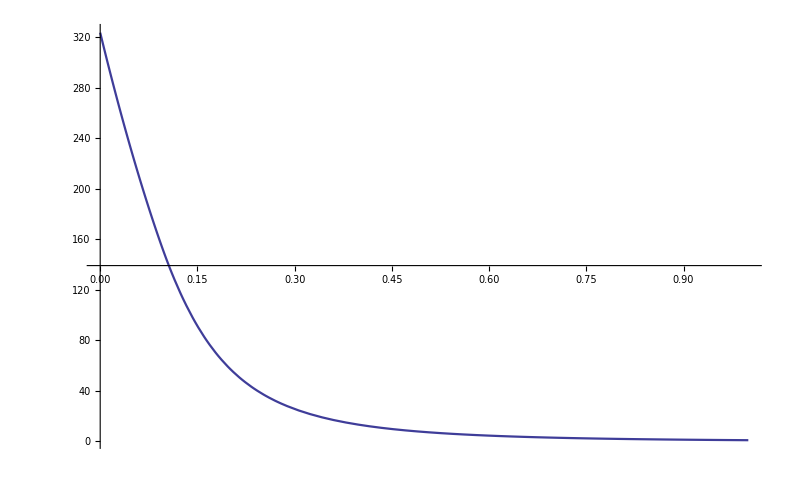

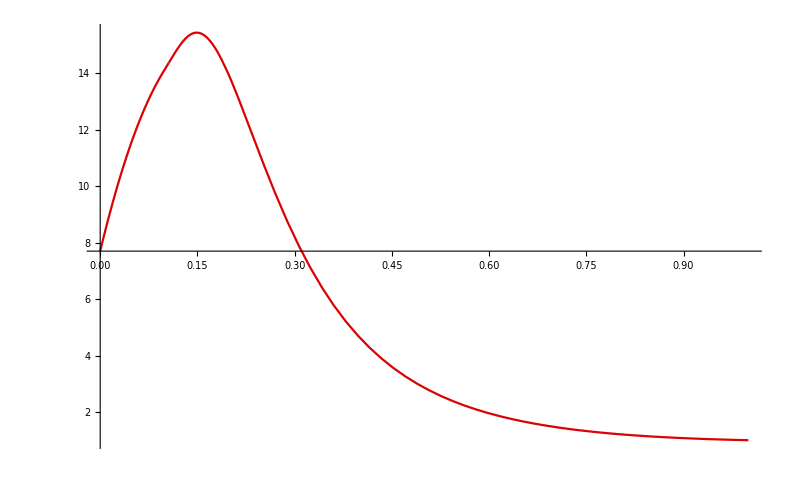

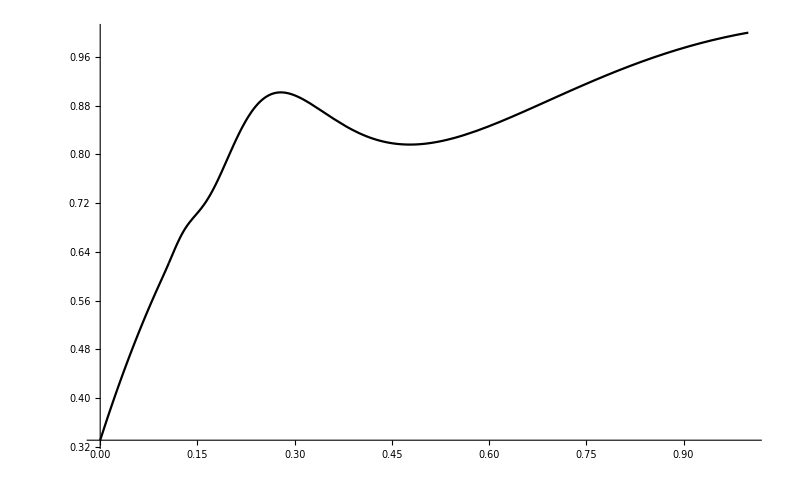

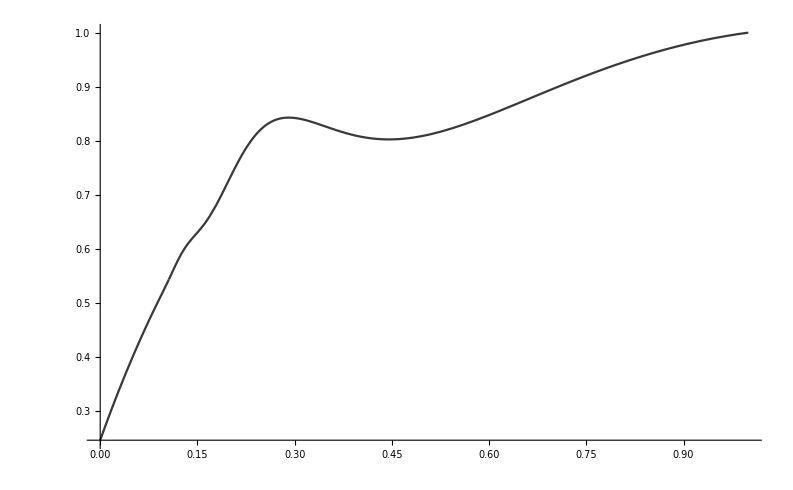

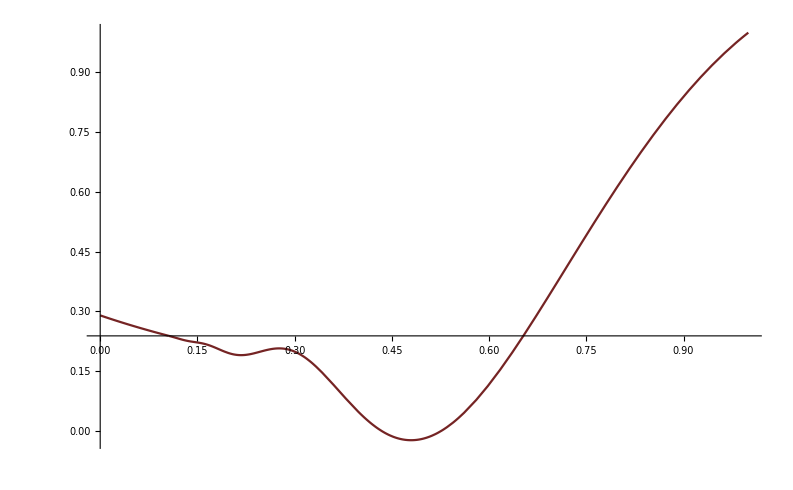

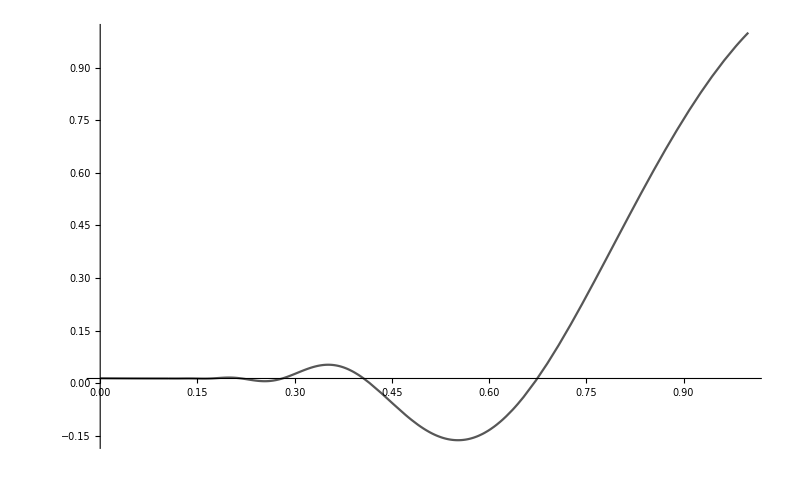

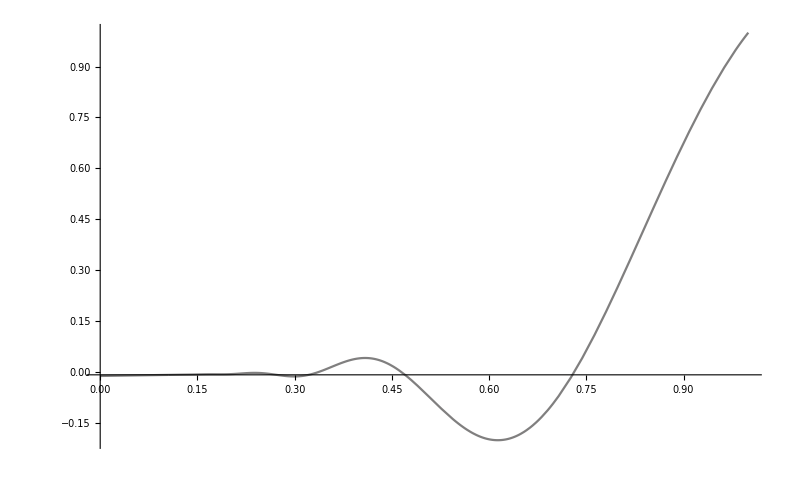

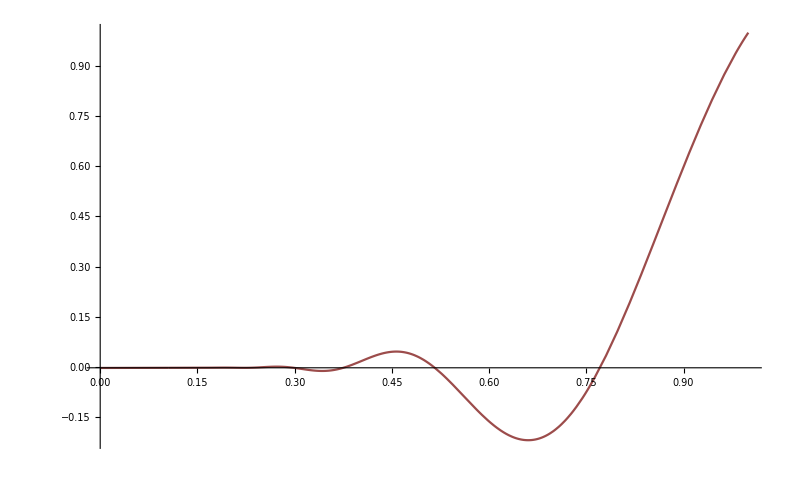

```mathematica
Show[Plot$ϕQNM$Func$dom0[[1]],Plot$ϕQNM$Func$dom1[[1]]]
Show[Plot$ϕQNM$Func$dom0[[2]],Plot$ϕQNM$Func$dom1[[2]]]
Show[Plot$ϕQNM$Func$dom0[[3]],Plot$ϕQNM$Func$dom1[[3]]]
Show[Plot$ϕQNM$Func$dom0[[4]],Plot$ϕQNM$Func$dom1[[4]]]
Show[Plot$ϕQNM$Func$dom0[[5]],Plot$ϕQNM$Func$dom1[[5]]]
Show[Plot$ϕQNM$Func$dom0[[6]],Plot$ϕQNM$Func$dom1[[6]]]
Show[Plot$ϕQNM$Func$dom0[[7]],Plot$ϕQNM$Func$dom1[[7]]]
Show[Plot$ϕQNM$Func$dom0[[8]],Plot$ϕQNM$Func$dom1[[8]]]
Show[Plot$ϕQNM$Func$dom0[[9]],Plot$ϕQNM$Func$dom1[[9]]]
```

## QNM Amplitudes

## QNM Excitation Operators

### Operators

```mathematica
A$dom0[s_]:=- W$dom0*s^2*Id$dom0 + L1$dom0 + s*L2$dom0;
c$dom0[s_, sQNM_]:=L2$dom0- W$dom0*(s+sQNM)*Id$dom0;
B$dom0[s_,V0_,W0_]:=L2$dom0 . V0 - W$dom0*(s*V0 + W0);

A$dom1[s_]:=- W$dom1*s^2*Id$dom1 + L1$dom1 + s*L2$dom1;
c$dom1[s_, sQNM_]:=L2$dom1- W$dom1*(s+sQNM)*Id$dom1;
B$dom1[s_,V0_,W0_]:=L2$dom1 . V0 - W$dom1*(s*V0 + W0);
```

#### Choose QNM

```mathematica
An$dom0=Table[A$dom0[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom0=Table[c$dom0[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom0[[iQNM]],{iQNM,1,n$QNM$max}];

An$dom1=Table[A$dom1[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom1=Table[c$dom1[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom1[[iQNM]],{iQNM,1,n$QNM$max}];

(*An$Conj=Table[A[s$QNM$Conj[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$Conj=Table[c[s$QNM$Conj[[iQNM]],s$QNM$Conj[[iQNM]]].ϕQNM$Conj$Vec[[iQNM]],{iQNM,1,n$QNM$max}];*)
```

#### Multidomain Matrix

```mathematica
An=Table[ N[ArrayFlatten[{
{   An$dom0[[iQNM]]    ,       Zero$dom0dom1   } , 
{  Zero$dom1dom0,   An$dom1[[iQNM]] } 
}],
Prec],
{iQNM,1,n$QNM$max}
];




Cn=Table[ Join[Cn$dom0[[iQNM]],Cn$dom1[[iQNM]]],{iQNM,1,n$QNM$max}];
```

#### Continuity of Auxiliary function at Boundary Domain

```mathematica
An[[All,1,All]]=0;
An[[All,1,1]]=1;
An[[All,1,-1]]=-1;

Cn[[All,1]]=0;
```

#### Continuity of Auxiliary function’s derivative at Boundary Domain

```mathematica
An[[All,nz$dom0 + nz$dom1,All]]=0;
An[[All,nz$dom0 + nz$dom1, ;;nz$dom0]]=Dσ$dom0[[1, All]];
An[[All,nz$dom0 + nz$dom1, nz$dom0+1;;nz$dom0+nz$dom1 ]]=-Dσ$dom1[[-1, All]];

Cn[[All,-1]]=0;
```

### Amplitude Matrix

```mathematica
m1t =Table[Join[Transpose@An[[iQNM]], {Cn[[iQNM]]}],{iQNM,1,n$QNM$max}];
m1 =Table[Transpose[m1t[[iQNM]]],{iQNM,1,n$QNM$max}];

δ=Table[KroneckerDelta[i,nz$dom0+1],{i,1,nz$dom0+nz$dom1+1}];

Mamp=Table[Join[m1[[iQNM]], {δ}],{iQNM,1,n$QNM$max}];
MampInv=ParallelTable[Inverse@Mamp[[iQNM]],{iQNM,1,n$QNM$max}];


(*m1t$Conj=Table[Join[Transpose@An$Conj[[iQNM]], {Cn$Conj[[iQNM]]}],{iQNM,1,n$QNM$max}];
m1$Conj =Table[Transpose[m1t$Conj[[iQNM]]],{iQNM,1,n$QNM$max}];

Mamp$Conj=Table[Join[m1$Conj[[iQNM]], {δ}],{iQNM,1,n$QNM$max}];
Mamp$ConjInv=ParallelTable[Inverse@Mamp$Conj[[iQNM]],{iQNM,1,n$QNM$max}];*)
```

## Calculate QNM Amplitude

### Initial Data

```mathematica
ϕ0$dom0=ConstantArray[1,nz$dom0]; (*2*Re[ϕQNM$dom0];*) 
ψ0$dom0=ConstantArray[0,nz$dom0];(*2*Re[ϕQNM$dom0*s$QNM];*) 

ϕ0$dom1=ConstantArray[1,nz$dom1]; (*2*Re[ϕQNM$dom1];*) 
ψ0$dom1= ConstantArray[0,nz$dom1];(*2*Re[ϕQNM$dom1*s$QNM];*)
```

#### Source Function ID

```mathematica
Bn$dom0=Table[B$dom0[s$QNM[[iQNM]],ϕ0$dom0,ψ0$dom0],{iQNM,1,n$QNM$max}];
Bn$dom1=Table[B$dom1[s$QNM[[iQNM]],ϕ0$dom1,ψ0$dom1],{iQNM,1,n$QNM$max}];

Bn=Table[Join[Bn$dom0[[iQNM]],Bn$dom1[[iQNM]]],{iQNM,1,n$QNM$max}];
(*Bn$Conj=Table[B[s$QNM$Conj[[iQNM]],ϕ0,ψ0],{iQNM,1,n$QNM$max}];*)

Bn[[All,1]]=0;
Bn[[All,-1]]=0;
```

### Total Source

```mathematica
g0=1;

S=Table[Append[Bn[[iQNM]] , g0],{iQNM,1,n$QNM$max}];
(*S$Conj=Table[Append[Bn$Conj[[iQNM]] +S2ndOrder$Vec[s$QNM$Conj[[iQNM]]], g0],{iQNM,1,n$QNM$max}];*)
```

#### Amplitude

```mathematica
ηSol=Table[MampInv[[iQNM]].S[[iQNM]],{iQNM,1,n$QNM$max}];

η=ηSol[[All,nz$dom0+nz$dom1+1]];


ϕScri=ϕQNM$dom0[[All,nz$dom0]];
ϕHrz=ϕQNM$dom1[[All,1]];

ηϕScri=Table[ η[[iQNM]] * ϕScri[[iQNM]],{iQNM,1,n$QNM$max}];
ηϕHrz =Table[ η[[iQNM]] * ϕHrz[[iQNM]],{iQNM,1,n$QNM$max}];

ηϕScri;
Abs[ηϕHrz];
```

```mathematica
N[η]
```

{-0.0000492369-0.0000390543 ⅈ,-0.000449479-0.00134117 ⅈ,-4.1318-2.50642 ⅈ,4.34149-2.94025 ⅈ,0.279383-0.489568 ⅈ,1.40915+0.330781 ⅈ,3.2075+2.67673 ⅈ,-1.42852+13.0459 ⅈ,-39.2184+19.1481 ⅈ}

```mathematica
N[s$QNM,15]
N[ηϕScri,15]
(*N[Abs[ηϕScri]]
N[Arg[ηϕScri]]*)
```

{-0.304656296507759-0.16240670607899 ⅈ,-0.25115559975442-0.433142970449008 ⅈ,-0.21723470956909-0.736312554067186 ⅈ,-0.2116451411183+0.739198432707846 ⅈ,-0.36968030326643+0.971584358308218 ⅈ,-0.48018553877026-1.18411031663162 ⅈ,-0.588012334595+1.40296064781598 ⅈ,-0.6936978669852+1.62596077551055 ⅈ,-0.79774760368265+1.85164885509924 ⅈ}

{-0.021771383436852-0.0052589078796822 ⅈ,-0.0414597401459431+0.002412744922624 ⅈ,-5.58266863087+6.1205573739506 ⅈ,5.8939166560548+6.39753839183006 ⅈ,0.051713361715529-0.158441956624159 ⅈ,-0.0009723173367098+0.0953877204910092 ⅈ,-0.012380199885294-0.0616709430282314 ⅈ,-0.013893752486445-0.0440567956833934 ⅈ,-0.013433842888257-0.0341549921865974 ⅈ}

```mathematica
sA=s$QNM[[3]]
csA=Conjugate[sA]
ηA=ηϕScri[[3]]
cηA=Conjugate[ηA]
```

-0.21723470956908508137851908612804350326402796729166612897067857265210366656153883527939279900118278952027687944910756612245175749857976432123882332713421202-0.7363125540671859417784672389040264754426714684417051197621817949455621927485636955146665400221693758446440700016625869127878744275564348138051270672608214 ⅈ

-0.21723470956908508137851908612804350326402796729166612897067857265210366656153883527939279900118278952027687944910756612245175749857976432123882332713421202+0.7363125540671859417784672389040264754426714684417051197621817949455621927485636955146665400221693758446440700016625869127878744275564348138051270672608214 ⅈ

-5.5826686308700086521024192897781154590630450992984248755759207651830654963872000240268692921637257261008121478636831544242654918036662321569137+6.120557373950599294441484471511349764317588167219947611946064147021648566639095091129258622279416422554022072922122679122458287845521952715986 ⅈ

-5.5826686308700086521024192897781154590630450992984248755759207651830654963872000240268692921637257261008121478636831544242654918036662321569137-6.120557373950599294441484471511349764317588167219947611946064147021648566639095091129258622279416422554022072922122679122458287845521952715986 ⅈ

```mathematica
csB=s$QNM[[4]]
sB=Conjugate[csB]
cηB=ηϕScri[[4]]
ηB=Conjugate[cηB]
```

-0.2116451411183049057706762106223635572534131234672284606286025965653913979630384882473688118595513078748405290413293350380061205163470414047391215176122135+0.7391984327078456282195297917706771093215200019673262304849934541529971861748869748028918141738568964871713679212111365145396862659936367728508555460240967 ⅈ

-0.2116451411183049057706762106223635572534131234672284606286025965653913979630384882473688118595513078748405290413293350380061205163470414047391215176122135-0.7391984327078456282195297917706771093215200019673262304849934541529971861748869748028918141738568964871713679212111365145396862659936367728508555460240967 ⅈ

5.8939166560548061395785212028774977762759071907472137812384835414338432556186760860690251530452239679649530275833360856297639251201811764284106+6.3975383918300600018452872737365352116179668574593691882278194503660312557439318771018963222425159677217612185600799572588162072401994987177845 ⅈ

5.8939166560548061395785212028774977762759071907472137812384835414338432556186760860690251530452239679649530275833360856297639251201811764284106-6.3975383918300600018452872737365352116179668574593691882278194503660312557439318771018963222425159677217612185600799572588162072401994987177845 ⅈ

```mathematica
sA//N
sB//N
ηA//N
ηB//N
```

-0.217235-0.736313 ⅈ

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Conjugate[TerminatedEvaluation[RecursionLimit]]

-5.58267+6.12056 ⅈ

5.89392-6.39754 ⅈ

```mathematica
sA//N
csB//N
ηA//N
cηB//N
```

-0.217235-0.736313 ⅈ

-0.211645+0.739198 ⅈ

-5.58267+6.12056 ⅈ

5.89392+6.39754 ⅈ

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

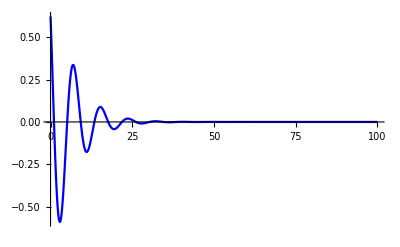

```mathematica
TimeSignal$Real=2*Re[ ηA*Exp[sA*τ]+ cηB*Exp[csB*τ]];


TimeSignal$Symmetric= ηA*Exp[sA*τ]+  cηA*Exp[csA*τ]+ ηB*Exp[sB*τ]+ cηB*Exp[csB*τ];
Plot[{TimeSignal$Real,TimeSignal$Symmetric},{τ,0,100}, PlotRange->All, PlotStyle->{Blue,Red}]
```

```mathematica
TimeSignal$RegARegB=ηA*Exp[sA*τ]+ ηB*Exp[sB*τ];
TimeSignal$RegAMirrB=ηA*Exp[sA*τ]+ cηB*Exp[csB*τ];
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

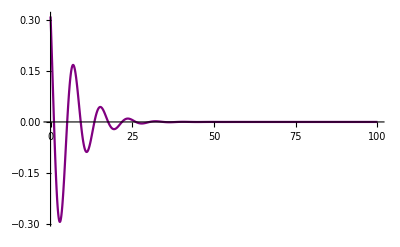

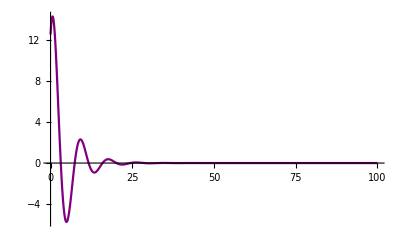

-Graphics-

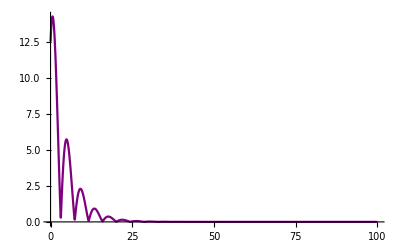

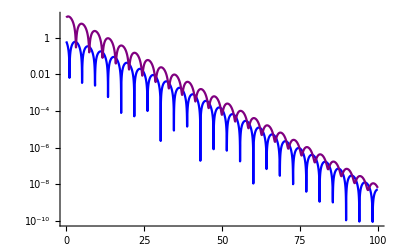

```mathematica
Plot[{Re@TimeSignal$Symmetric,Re@TimeSignal$RegARegB,Re@TimeSignal$RegAMirrB},{τ,0,100}, PlotRange->All, PlotStyle->{Red,Gray, Purple}]
Plot[{Im@TimeSignal$Symmetric,Im@TimeSignal$RegARegB,Im@TimeSignal$RegAMirrB},{τ,0,100}, PlotRange->All, PlotStyle->{Red,Gray, Purple}]

Plot[{Abs@TimeSignal$Symmetric,Abs@TimeSignal$RegARegB},{τ,0,100}, PlotRange->All, PlotStyle->{Red,Gray}]
Plot[{Abs@TimeSignal$Symmetric,Abs@TimeSignal$RegAMirrB},{τ,0,100}, PlotRange->All, PlotStyle->{Red,Purple}]


LogPlot[{Abs@TimeSignal$Real,Abs@TimeSignal$Symmetric,Abs@TimeSignal$RegARegB,Abs@TimeSignal$RegAMirrB},{τ,0,100}, PlotRange->All, PlotStyle->{Blue,Red, Gray, Purple}]
```

-Graphics-

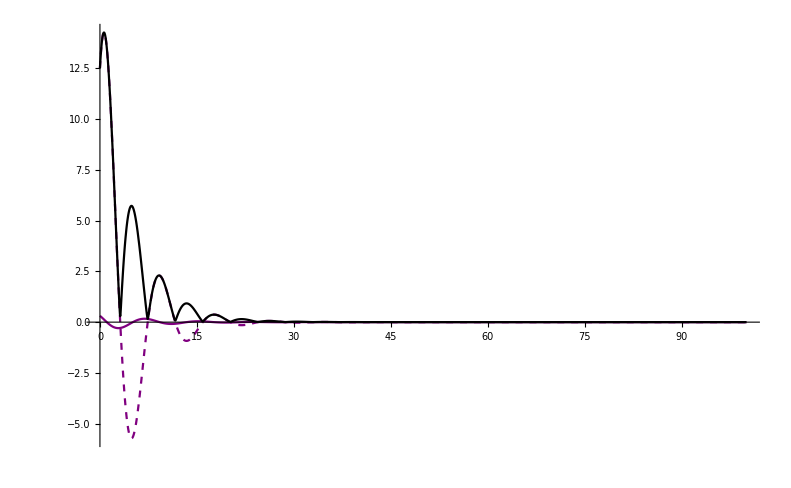

```mathematica
Plot[{Re@TimeSignal$RegARegB,Im@TimeSignal$RegARegB,Abs@TimeSignal$RegARegB},{τ,0,100}, PlotRange->All, PlotStyle->{{Gray},{Gray,Dashed}, {Black}}]
Plot[{Re@TimeSignal$RegAMirrB,Im@TimeSignal$RegAMirrB,Abs@TimeSignal$RegAMirrB},{τ,0,100}, PlotRange->All, PlotStyle->{{Purple},{Purple,Dashed}, {Black}}]
```

```mathematica
s0=s$QNM[[4]]
ρ0=Abs[ηϕScri[[4]]]
ϕ0=Arg[ηϕScri[[4]]]
```

-0.2116451411183049057706762106223635572534131234672284606286025965653913979630384882473688118595513078748405290413293350380061205163470414047391215176122135+0.7391984327078456282195297917706771093215200019673262304849934541529971861748869748028918141738568964871713679212111365145396862659936367728508555460240967 ⅈ

8.6986637493042469202417013302123466816403722288419034049265264549672959185946726893518959043450940501410217385226635470963634029758881593306227

0.82634857882369326289961801636011640430645992575110698262295932658933417107748721040624362245966078957118372512634031233013054245407084791283781

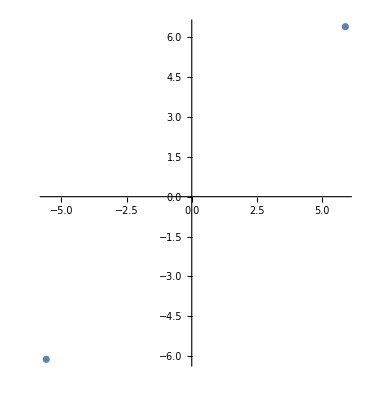

```mathematica
ComplexListPlot[{ηϕScri[[4]],Conjugate@ηϕScri[[3]]}]
```

```mathematica
s1=Conjugate[s$QNM[[3]]]
ρ1=Abs[Conjugate[ηϕScri[[3]]]]
ϕ1=Arg[Conjugate[ηϕScri[[3]]]]

(*s1=s$QNM[[4]]
ρ1=Abs[ηϕScri[[4]]]
ϕ1=Arg[ηϕScri[[4]]]*)
```

-0.21723470956908508137851908612804350326402796729166612897067857265210366656153883527939279900118278952027687944910756612245175749857976432123882332713421202+0.7363125540671859417784672389040264754426714684417051197621817949455621927485636955146665400221693758446440700016625869127878744275564348138051270672608214 ⅈ

8.2841663195472526130439848959708082628759229819134995469477005397175949053276403055243694801464543234060075180653175111471180594220287714516502

-2.3102660872977242940692557594521528469191036011519636266132838543389763580075983024869375883855370781124657703120552835014419094102531619924518

```mathematica
δs=s1-s0
δsR=Re[δs]
δsI=Im[δs]
δρ=ρ1-ρ0
δϕ=ϕ0-ϕ1-π
 
 sR=-Re[s0];
 sI=Im[s0];
```

-0.00558956845078017560784287550567994601061484382443766834207597608671226859850034703202398714163148164543635040777823108444563698223272291649970180952199852-0.0028858786406596864410625528666506338788485335256211107228116592074349934263232792882252741516875206425272979195485496017518118384372019590457284787632754 ⅈ

-0.00558956845078017560784287550567994601061484382443766834207597608671226859850034703202398714163148164543635040777823108444563698223272291649970180952199852

-0.0028858786406596864410625528666506338788485335256211107228116592074349934263232792882252741516875206425272979195485496017518118384372019590457284787632754

-0.414497429756994307197716434241538418764449246928403857978825915249701013267032383827526424198639726735014220457346035949245343553859387878973

-0.0049779874683756814937696074672336329716058724720352117387014113795058772011234857348536144969192002984985910748867108155213927452265723264358

Dependence of ηϕScri on (ϵ,ao)

```mathematica
(*ηSol$Conj=Table[Mamp$ConjInv[[iQNM]].S$Conj[[iQNM]],{iQNM,1,n$QNM$max}];
η$Conj=ηSol$Conj[[All,Nz+2]];
ϕScri$Conj=ϕQNM$Conj$Vec[[All,nz]];
ϕHrz$Conj=ϕQNM$Conj$Vec[[All,1]];

ηϕScri$Conj=Table[η$Conj[[iQNM]]*ϕScri$Conj[[iQNM]],{iQNM,1,n$QNM$max}];
ηϕHrz$Conj=Table[η$Conj[[iQNM]]*ϕHrz$Conj[[iQNM]],{iQNM,1,n$QNM$max}];

Abs[ηϕScri$Conj]
Abs[ηϕHrz$Conj]*)
```

## Comparison Against Time Evolution

## Exact QNMs Contributions

```mathematica
hQNM$Scri[τ_, n_]:= 2*Re[ ηϕScri[[n]]*Exp[s$QNM[[n]]*τ]] (*+ ηϕScri$Conj[[n+1]]*Exp[s$QNM$Conj[[n+1]]*τ];*)
hQNM$Hrz[τ_, n_]:= 2* Re[ηϕHrz[[n]]*Exp[s$QNM[[n]]*τ]](* + ηϕHrz$Conj[[n+1]]*Exp[s$QNM$Conj[[n+1]]*τ];*)



PlotFreqEvol = Table[ LogPlot[Abs@hQNM$Scri[τ,iQNM], {τ,0,100}, WorkingPrecision->100, PlotLabels->{"sQNM_"<>ToString[iQNM-1]}, PlotStyle->ColorData[iQNM,"ColorList"], PlotRange->All], {iQNM, 1,n$QNM$max }];

Show[PlotFreqEvol]
```

-Graphics-

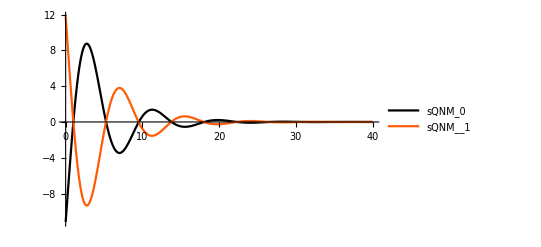

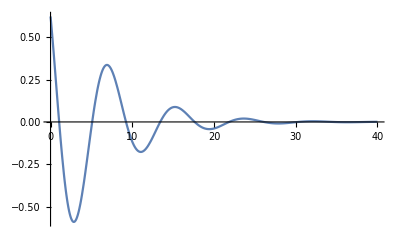

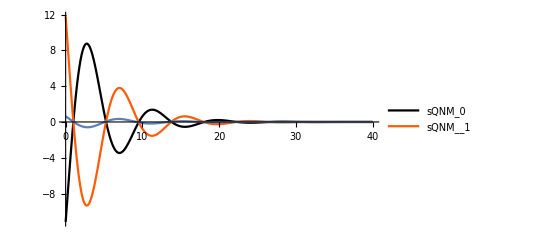

```mathematica
PlotFreqEvol =  Plot[{hQNM$Scri[τ,3],hQNM$Scri[τ,4]}, {τ,0,40}, WorkingPrecision->100, PlotLegends->{{"sQNM_0","sQNM__1"}}, PlotStyle->ColorData[3,"ColorList"], PlotRange->All]
PlotFreqEvolSum =  Plot[hQNM$Scri[τ,3]+hQNM$Scri[τ,4], {τ,0,40}, WorkingPrecision->100,  PlotRange->All]

Show[PlotFreqEvol,PlotFreqEvolSum]
```

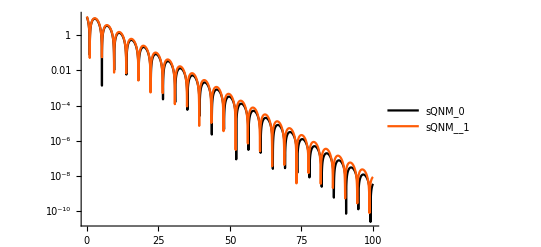

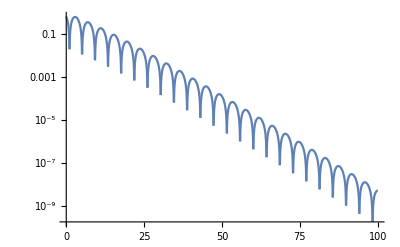

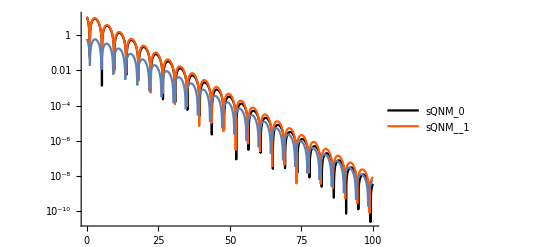

```mathematica
PlotFreqEvol =  LogPlot[{Abs@hQNM$Scri[τ,3],Abs@hQNM$Scri[τ,4]}, {τ,0,100}, WorkingPrecision->100, PlotLegends->{{"sQNM_0","sQNM__1"}}, PlotStyle->ColorData[3,"ColorList"], PlotRange->All]
PlotFreqEvolSum =  LogPlot[Abs[hQNM$Scri[τ,3]+hQNM$Scri[τ,4]], {τ,0,100}, WorkingPrecision->100,  PlotRange->All]

Show[PlotFreqEvol,PlotFreqEvolSum]
```

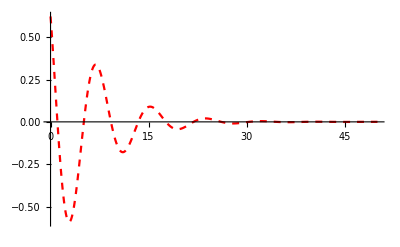

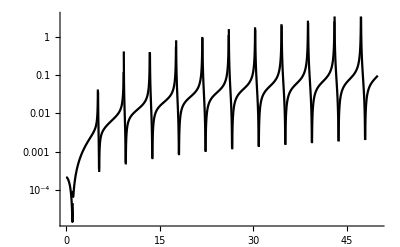

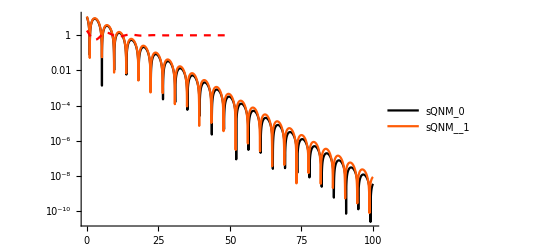

```mathematica
h$Interference=-2*(ⅇ^(-sR τ) (δρ (1+δsR τ) (1+δsI δϕ τ)+ρ0 τ (δsR+δsI δϕ+δsI δsR δϕ τ)) Cos[sI τ+ϕ0]+ⅇ^(-sR τ) (δρ+ρ0) (δϕ-δsI τ) (1+δsR τ) Sin[sI τ+ϕ0]);
PlotInterference=Plot[h$Interference,{τ,0,50}, PlotStyle->{Red,Dashed}, PlotRange->All]
InterferenceError=Abs[1-h$Interference/(hQNM$Scri[τ,3]+hQNM$Scri[τ,4])];
PlotError=LogPlot[InterferenceError,{τ,0,50}, PlotStyle->{Black}, PlotRange->All]
Show[PlotFreqEvol,PlotInterference]
```

## Load Time Evolution Data

```mathematica
Print["Load data"];

n$QNM$FirstOrder=0;
WaveDataFile=DirName<>"../data/CteField/spin_"<>ToString[spin]<>"/l_"<>ToString[l]<>"/epsilon_"<>ToString[NumberForm[N[ϵ],{7,6},NumberPadding->{"","0"}]]<>"_a0_"<>ToString[NumberForm[N[ao],{7,6},NumberPadding->{"","0"}]]<>"/N0_5_N1_100_ndom_4_nfields_2/gnuplot2D_field_0_dom_0.dat"
WaveDataRaw1=Import[WaveDataFile, "Table"];

WaveDataHeader1=WaveDataRaw1[[1]]
WaveData1=Delete[WaveDataRaw1,1];
NWave=Length@WaveData1
Time=WaveData1[[All,1]];
h=Time[[2]]-Time[[1]]
hScri=WaveData1[[All,2]];
hHrz=WaveData1[[All,22]];

hQNM$Hrz$ExactData=.
hQNM$Hrz$ExactData[n_]:=hQNM$Hrz[Time,n+1];


hQNM$Scri$ExactData=.
hQNM$Scri$ExactData[n_]:=hQNM$Scri[Time,n+1];
```

Load data

/Users/qtc325/Trabalhos/NBIA/2024_09_QNMResonantExcitation_ElephantFlea/SphericalSym_ElephFlea_TimeEvol/ExternalCodes/../data/CteField/spin_2/l_2/epsilon_0.002040_a0_11.572200/N0_5_N1_100_ndom_4_nfields_2/gnuplot2D_field_0_dom_0.dat

{#1:T,#2:0.000e+00,#3:4.424e-03,#4:7.870e-03,#5:1.055e-02,#6:1.264e-02,#7:1.427e-02,#8:1.554e-02,#9:1.653e-02,#10:1.730e-02,#11:1.790e-02,#12:1.837e-02,#13:1.874e-02,#14:1.902e-02,#15:1.925e-02,#16:1.943e-02,#17:1.957e-02,#18:1.968e-02,#19:1.978e-02,#20:1.986e-02,#21:1.993e-02,#22:2.000e-02}

5001

0.1

#### Map time to index

```mathematica
ti=Time[[1]]
tf=Time[[NWave]]
δt=tf-ti

IndxT[t_]:=Round[(NWave-1)*(t-ti)/δt+1 ];
```

0.

500.

500.

## Filtering QNM

Plot data

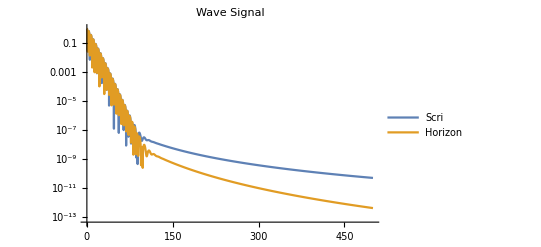

```mathematica
Print["Plot data"];
PlotWave=ListLogPlot[
{Transpose@{Time,Abs@hScri},
Transpose@{Time,Abs@hHrz}
},
PlotLabel->"Wave Signal",
PlotLegends->
{"Scri",
"Horizon"
},
Joined->True
];
Show[PlotWave]
```

### Study Wave

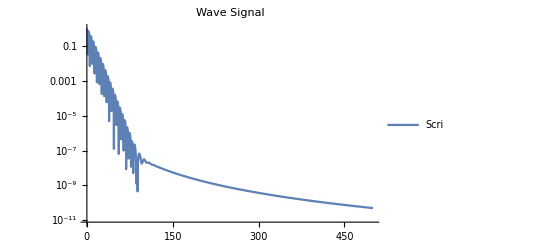

```mathematica
(*WaveBasis=hHrz;
SurfaceName="Horizon";*)

WaveBasis=hScri;
SurfaceName="Scri";

PlotStudy=ListLogPlot[
{Transpose@{Time,Abs@WaveBasis}
},
PlotLabel->"Wave Signal",
PlotLegends->{SurfaceName},
Joined->True
];
Show[PlotStudy]
```

Data Analysis (simple fit as easiest first option): 
(1) Blind test with unknown Amp and unknown ω
(2) Schwarzschild test with unknown Amp, but ω_Schwarz
(3) Elephant Flea test with unknown Amp, but ω_ElFlea

### Filter Fundamental QNM

```mathematica
WaveA= hQNM$Scri$ExactData[2] ;
WaveB= hQNM$Scri$ExactData[3];

Wave0= hQNM$Scri$ExactData[2] + hQNM$Scri$ExactData[3];


(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*hQNM$Scri$ExactData[3];*)
(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*Wave0=hQNM$Hrz$ExactData;*)

PlotExact=ListLogPlot[
{Transpose@{Time,Abs@WaveBasis},
Transpose@{Time,Abs@Wave0},
Transpose@{Time,Abs@WaveA},
Transpose@{Time,Abs@WaveB}
},
PlotLabels->{"Full Signal Num", "1stOrder-QNM (n=0) Exact", "n=0", , "n=1"},
PlotStyle->{{Black}, {Red}, {Blue, Dashed},{Green, Dashed}},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,110},{10^-10,10}},
ImageSize->Scaled[0.8]
];
Show[PlotExact]
```

-Graphics-

```mathematica
WaveFilter0 = WaveBasis - Wave0;
Wave1=hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5]+hQNM$Scri$ExactData[6]+hQNM$Scri$ExactData[7]+hQNM$Scri$ExactData[8];
(*hQNM$Scri$ExactData[2];*)
(*hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5];*)
(*hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5](*+hQNM$Scri$ExactData[6]*);*)
(*Wave1=hpp$HRz$ExactData*)

PlotFilter0=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter0},
(*Transpose@{Time,Abs@hpm$HRz$ExactData}*)
Transpose@{Time,Abs@Wave1}
},
(*PlotLabels->{"Residual Signal (n=0)" , "2ndOrder-QNM (+-) Exact"},*)
PlotLabels->{"Residual Signal (n=0)" , "1stOrder-QNM (n=1) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,80},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter0]
```

-Graphics-

### Filter First Overtone

```mathematica
WaveFilter1 =WaveFilter0-Wave1;
Wave2=hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5];
(*Wave2=hpm$HRz$ExactData;*)

PlotFilter1=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter1}(*,*)
(*Transpose@{Time,Abs@Wave2}*)
},
(*PlotLabels->{"Residual Signal (n=0, +-)" , "2ndOrder-QNM (++) Exact"},*)
PlotLabels->{"Residual Signal (n=0, n=1)" , "1stOrder-QNM (n=2) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,40},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter1]
```

-Graphics-

### Filter Second Overtone

```mathematica
WaveFilter2 =WaveFilter1 - Wave2;
(*Wave3=hQNM$Scri$ExactData[3];*)
PlotFilter2=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter2}(*,
Transpose@{Time,Abs@Wave3}*)
},
PlotLabels->{"Residual Signal (n=0, n=1, n=2)", "1stOrder-QNM (n=3) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,30},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter2]
```

-Graphics-

```mathematica
hFIT=A*exp(s0*t)+B*exp(s1*t)
```

A exp s0 t+B exp s1 t

(i) We known s0 and s1 from freq. domain. Fit for A and B. Do we recover prediction from ID? Guess: Yes
(ii) Blind agnostic test: fit for (A,B, s0, s1). Do we recover the avoid crossing QNMs? Guess: No ?

## “Fourier” Analysis Time Domain Signal - Poor Man Data Analysis

```mathematica
WaveStudy= WaveBasis;
(*Sum[hQNM$Scri$ExactData[i],{i,0,8}];*)(*hQNM$Scri$ExactData[1]+
hQNM$Scri$ExactData[2]+
hQNM$Scri$ExactData[3]+
hQNM$Scri$ExactData[4];*)
(*WaveBasis;*) (*Sum[hQNM$Scri$ExactData[i],{i,0,8}];*)

(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)

(*WaveBasis-(hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3]);*)


(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)(*WaveBasis;*)
(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*WaveBasis;*)

PlotTimeSignal=ListLogPlot[
{Transpose@{Time,Abs@WaveStudy}
},
PlotLabel->"Wave Signal",
PlotLegends->
{"Scri"},
Joined->True,
ImageSize->Scaled[0.8]
];
Show[PlotTimeSignal]
```

-Graphics-

### Select QNM phase

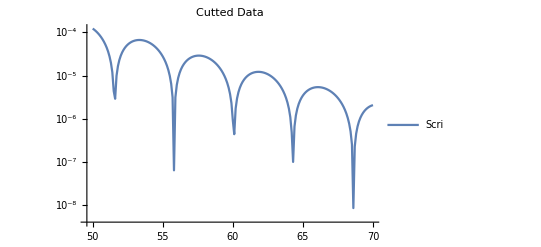

```mathematica
t0=50;I0=IndxT[t0];
t1=70; I1=IndxT[t1];
tData=Table[ Time[[i]],{i,I0,I1}];
Data=Table[WaveStudy[[i]],{i,I0,I1}];

NData=Length@Data;
PlotData=ListLogPlot[
{Transpose@{tData,Abs@Data}
},
PlotLabel->"Cutted Data",
PlotLegends->
{"Scri"},
Joined->True
];
Show[PlotData]
```

```mathematica
ACFitModel=ComplexExpand[(A1R+I A1I)(1+ t * (A2R+I A2I))*Exp[-I (wr+I wi) t]]/.I->ImagUnit
ACFitModelReal=Coefficient[ACFitModel,ImagUnit,0]
```

A1R ⅇ^(t wi) Cos[t wr]-A1I A2I ⅇ^(t wi) t Cos[t wr]+A1R A2R ⅇ^(t wi) t Cos[t wr]+A1I ⅇ^(t wi) Sin[t wr]+A1R A2I ⅇ^(t wi) t Sin[t wr]+A1I A2R ⅇ^(t wi) t Sin[t wr]+ImagUnit (A1I ⅇ^(t wi) Cos[t wr]+A1R A2I ⅇ^(t wi) t Cos[t wr]+A1I A2R ⅇ^(t wi) t Cos[t wr]-A1R ⅇ^(t wi) Sin[t wr]+A1I A2I ⅇ^(t wi) t Sin[t wr]-A1R A2R ⅇ^(t wi) t Sin[t wr])

A1R ⅇ^(t wi) Cos[t wr]-A1I A2I ⅇ^(t wi) t Cos[t wr]+A1R A2R ⅇ^(t wi) t Cos[t wr]+A1I ⅇ^(t wi) Sin[t wr]+A1R A2I ⅇ^(t wi) t Sin[t wr]+A1I A2R ⅇ^(t wi) t Sin[t wr]

```mathematica
Data2Fit=Transpose@{tData,Data};

nQNM$Fit=2;

(*model=Sum [ A[i]*Exp[-ωi[i] *t]Sin[ϕ[i]+ωr[i]*t] ,{i,1,nQNM$Fit}]
modelpar=Table[{A[i],ϕ[i],ωi[i], ωr[i]},{i,1,nQNM$Fit}]//Flatten*)

model=ACFitModelReal(*A[1](1+A[2]*t)*Exp[-ωi[1] *t]Sin[ϕ[1]+ωr[1]*t];*)
modelpar={A1R,A1I,A2R,A2I,wr,wi}(*{A[1],A[2],ωr[1],ωi[1], ϕ[1]};*)

(*model=A[1] t *Exp[-ωi[1] *t]Sin[ϕ[1]+ωr[1]*t];
modelpar={A[1],ωr[1],ωi[1], ϕ[1]};*)

N[ComplexExpand[WaveDoublePole],5]//Chop
nlm=NonlinearModelFit[Data2Fit,model,modelpar,t, MaxIterations->Infinity, AccuracyGoal->0.5*MachinePrecision, PrecisionGoal->0.5*MachinePrecision,  WorkingPrecision->MachinePrecision]//Normal
nlm$data=nlm/.t->tData;
Residual=Abs[Data-nlm$data]/Abs[Data];

FittedData=Transpose@{tData,nlm$data};
ResidualData=Transpose@{tData,Residual};

ListLogPlot[{Abs@Data2Fit,Abs@FittedData}, Joined->True, PlotLabels->{"Data", "Fit"}]
(*ListLogPlot[Abs@ResidualData, Joined->True, PlotLabels->{"Residual"}]*)
N@s$QNM
(*N@s$QNM[[3]]
N@s$QNM[[4]]


2*Abs[ηϕScri[[3]]]
2*Abs[ηϕScri[[4]]]

π+Arg[ηϕScri[[3]]]
π+Arg[ηϕScri[[4]]]*)
```

A1R ⅇ^(t wi) Cos[t wr]-A1I A2I ⅇ^(t wi) t Cos[t wr]+A1R A2R ⅇ^(t wi) t Cos[t wr]+A1I ⅇ^(t wi) Sin[t wr]+A1R A2I ⅇ^(t wi) t Sin[t wr]+A1I A2R ⅇ^(t wi) t Sin[t wr]

{A1R,A1I,A2R,A2I,wr,wi}

0.6225 2.7183^(-0.21444 t) Cos[0.73776 t]+0.028023 2.7183^(-0.21444 t) t Cos[0.73776 t]-0.55396 2.7183^(-0.21444 t) Sin[0.73776 t]-0.10309 2.7183^(-0.21444 t) t Sin[0.73776 t]

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (MachinePrecision).

-1.44308×10^-38 ⅇ^(1. t) Cos[1. t]-7.88502×10^-39 ⅇ^(1. t) t Cos[1. t]-6.54577×10^-39 ⅇ^(1. t) Sin[1. t]-2.09766×10^-38 ⅇ^(1. t) t Sin[1. t]

-Graphics-

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ,-0.588012+1.40296 ⅈ,-0.693698+1.62596 ⅈ,-0.797748+1.85165 ⅈ}

```mathematica
sA=s$QNM[[4]]
csA=Conjugate[sA]
sB=s$QNM[[3]]
csB=Conjugate[sB]
sEP=(sA+sB)/2
```

-0.2116451411183049057706762106223635572534131234672284606286025965653913979630384882473688118595513078748405290413293350380061205163470414047391215176122135+0.7391984327078456282195297917706771093215200019673262304849934541529971861748869748028918141738568964871713679212111365145396862659936367728508555460240967 ⅈ

-0.2116451411183049057706762106223635572534131234672284606286025965653913979630384882473688118595513078748405290413293350380061205163470414047391215176122135-0.7391984327078456282195297917706771093215200019673262304849934541529971861748869748028918141738568964871713679212111365145396862659936367728508555460240967 ⅈ

-0.21723470956908508137851908612804350326402796729166612897067857265210366656153883527939279900118278952027687944910756612245175749857976432123882332713421202-0.7363125540671859417784672389040264754426714684417051197621817949455621927485636955146665400221693758446440700016625869127878744275564348138051270672608214 ⅈ

-0.21723470956908508137851908612804350326402796729166612897067857265210366656153883527939279900118278952027687944910756612245175749857976432123882332713421202+0.7363125540671859417784672389040264754426714684417051197621817949455621927485636955146665400221693758446440700016625869127878744275564348138051270672608214 ⅈ

-0.21443992534369499357459764837520353025872054537944729479964058460874753226228866176338080543036704869755870424521845058022893900746340286298897242237321276+0.0014429393203298432205312764333253169394242667628105553614058296037174967131616396441126370758437603212636489597742748008759059192186009795228642393816377 ⅈ

```mathematica
ηA=ηϕScri[[4]]
cηA=Conjugate[ηA]
ηB=ηϕScri[[3]]
cηB=Conjugate[ηB]
```

5.8939166560548061395785212028774977762759071907472137812384835414338432556186760860690251530452239679649530275833360856297639251201811764284106+6.3975383918300600018452872737365352116179668574593691882278194503660312557439318771018963222425159677217612185600799572588162072401994987177845 ⅈ

5.8939166560548061395785212028774977762759071907472137812384835414338432556186760860690251530452239679649530275833360856297639251201811764284106-6.3975383918300600018452872737365352116179668574593691882278194503660312557439318771018963222425159677217612185600799572588162072401994987177845 ⅈ

-5.5826686308700086521024192897781154590630450992984248755759207651830654963872000240268692921637257261008121478636831544242654918036662321569137+6.120557373950599294441484471511349764317588167219947611946064147021648566639095091129258622279416422554022072922122679122458287845521952715986 ⅈ

-5.5826686308700086521024192897781154590630450992984248755759207651830654963872000240268692921637257261008121478636831544242654918036662321569137-6.120557373950599294441484471511349764317588167219947611946064147021648566639095091129258622279416422554022072922122679122458287845521952715986 ⅈ

```mathematica
cηB
```

-5.5826686308700086521024192897781154590630450992984248755759207651830654963872000240268692921637257261008121478636831544242654918036662321569137-6.120557373950599294441484471511349764317588167219947611946064147021648566639095091129258622279416422554022072922122679122458287845521952715986 ⅈ

```mathematica
BEP=(ηA+cηB)
cBEP=Conjugate[BEP];

bb=(cηB-ηA)/(BEP)*(csB-sA)/(2*sEP);
cbb=Conjugate[bb];

sEP=(sA+csB)/2
csEP=Conjugate[sEP];
```

0.311248025184797487476101913099382317212862091448788905662562776250777759231476062042155860881498241864140879719652931205498433316514944271497+0.276981017879460707403802802225185447300378690239421576281755303344382689104836785972637699963099545167739145637957278136357919394677546001799 ⅈ

-0.21443992534369499357459764837520353025872054537944729479964058460874753226228866176338080543036704869755870424521845058022893900746340286298897242237321276+0.737755493387515784998998515337351792382095735204515675123587624549279689461725335158779177098013136165907718961436861713663780346775035793327991306642459 ⅈ

```mathematica
WaveSimplePole=(ηA*Exp[sA*t]+cηA*Exp[csA*t]+ηB*Exp[sB*t]+cηB*Exp[csB*t]);

WaveDoublePole=BEP*(1+  bb * sEP * t)Exp[sEP*t]+cBEP*(1+  cbb * csEP * t)Exp[csEP*t];
WaveLinear=BEP*( (*1+ *) bb * sEP * t)Exp[sEP*t]+cBEP*((*1+ *) cbb * csEP * t)Exp[csEP*t];


PlotSimplePole=LogPlot[Abs@WaveSimplePole,{t,0,100}, PlotRange->All, PlotStyle->Red, PlotLabels->"Simple Pole Model"];
PlotDoublePole=LogPlot[Abs@WaveDoublePole,{t,0,100}, PlotRange->All, PlotStyle->Orange, PlotLabels->"Double Pole Model"];
PlotLinear=LogPlot[Abs@WaveLinear,{t,0,100}, PlotRange->All, PlotStyle->Brown, PlotLabels->"Double Pole Model"];

PlotSimplePoleData=ListLogPlot[Transpose@{Time,Abs@Wave0}, PlotRange->{{0,110},{10^-10,10}}, PlotStyle->Green, PlotLabels->"Simple Pole Model",Joined->True];

PlotBasis=ListLogPlot[Transpose@{Time,Abs@WaveBasis}, PlotRange->{{8,70},{10^-10,10}},Joined->True, PlotLabels->{"Data"}];
PlotDataFit=ListLogPlot[Transpose@{tData,Abs@Data}, Joined->True, PlotLabels->{"Data Fit"}, PlotStyle->Purple];

(*Show[PlotSimplePole,PlotDoublePole ]
Show[PlotBasis,PlotDataFit,PlotSimplePole ]*)
Show[PlotBasis,PlotDoublePole ]
Show[PlotBasis,PlotLinear ]
(*Show[PlotBasis,PlotSimplePoleData]
Show[PlotSimplePole,PlotSimplePoleData]*)
```

-Graphics-

-Graphics-

```mathematica
N[ComplexExpand[WaveDoublePole],5]//Chop
ACFitModelReal
nlm
```

0.6225 2.7183^(-0.21444 t) Cos[0.73776 t]+0.028023 2.7183^(-0.21444 t) t Cos[0.73776 t]-0.55396 2.7183^(-0.21444 t) Sin[0.73776 t]-0.10309 2.7183^(-0.21444 t) t Sin[0.73776 t]

A1R ⅇ^(t wi) Cos[t wr]-A1I A2I ⅇ^(t wi) t Cos[t wr]+A1R A2R ⅇ^(t wi) t Cos[t wr]+A1I ⅇ^(t wi) Sin[t wr]+A1R A2I ⅇ^(t wi) t Sin[t wr]+A1I A2R ⅇ^(t wi) t Sin[t wr]

-0.0382181 ⅇ^(-0.150577 t) Cos[0.736914 t]+0.00101374 ⅇ^(-0.150577 t) t Cos[0.736914 t]+0.008529 ⅇ^(-0.150577 t) Sin[0.736914 t]-0.000165535 ⅇ^(-0.150577 t) t Sin[0.736914 t]

```mathematica
WaveSimplePole/.t->0
```

6.0495406686472048833165721594271889348823382364716082340697649295592321352344141170901030834859730888970234674431625512325131417784386485641591-0.138490508939730353701901401112592723650189345119710788140877651672191344552418392986318849981549772583869572818978639068178959697338773000899 ⅈ

Data with nModes:
 - fit with nFit = nModes reproduce the correct values
- fit with nFit < nModes don’t reproduce
- fit with nFit > nModes reproduce the correct values, but with double counting within numerical error

But real data has nModes --> ∞ and also Branch Cut (tail decay) contaminating the data. Therefore fit doesn’t work

ⅇ^(-t ωi[1]) A[1] Sin[ϕ[1]+t ωr[1]]+ⅇ^(-t ωi[2]) A[2] Sin[ϕ[2]+t ωr[2]]+ⅇ^(-t ωi[3]) A[3] Sin[ϕ[3]+t ωr[3]]

{A[1],ϕ[1],ωi[1],ωr[1],A[2],ϕ[2],ωi[2],ωr[2],A[3],ϕ[3],ωi[3],ωr[3]}

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (MachinePrecision).

0.0830598 ⅇ^(-0.251156 t) Sin[4.77052+0.433143 t]+16.5683 ⅇ^(-0.217235 t) Sin[5.54372+0.736313 t]+17.3973 ⅇ^(-0.211645 t) Sin[2.39714+0.739198 t]

-Graphics-

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ,-0.588012+1.40296 ⅈ,-0.693698+1.62596 ⅈ,-0.797748+1.85165 ⅈ}

```mathematica
sSchwarzschil$n0=-0.1779246313778724125652120005152178509675423181561187703639623721770992017316962715759234642097336789737598225764160641944325887735662226216980430348181479+I* 0.747343368836081044564012120434754107823160172903535881938910623355711335675523008900239525461539174202261286644053489464729872338914566586615874614796782;
N[sSchwarzschil$n0,3]
```

-0.18+0.747 ⅈ

```mathematica
N@s$QNM
```

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ}

### Fourier Analysis

#### Poor-man Routine to read local maximum

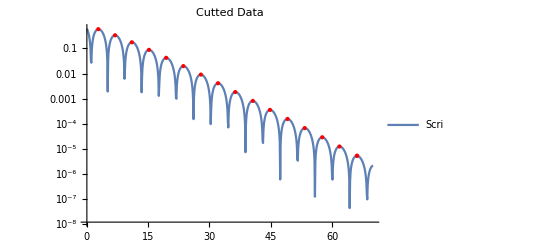

```mathematica
kmax=1;
kk=1;
MaxPos={};
While[kk<NData,
For[k=kmax+1, k<NData, k++,
Fm1=Abs@Data[[k-1]];
F=Abs@Data[[k]];
Fp1=Abs@Data[[k+1]];

If[F>Fm1 && F>Fp1,
kmaxt=k;
Break[];
];
];
kmax=kmaxt;
MaxPos=Append[MaxPos,kmax];
kk=k;
]
MaxSize=Length@MaxPos;
MaxData=Table[{tData[[MaxPos[[n]]]],Abs@Data[[MaxPos[[n]]  ]]}, {n,1,MaxSize}];
PlotMax=ListLogPlot[MaxData, PlotRange->Full, PlotStyle->{Red,PointSize[Medium]}];
Show[PlotData,PlotMax]
```

#### Fit Exponential

-0.18690669828540074

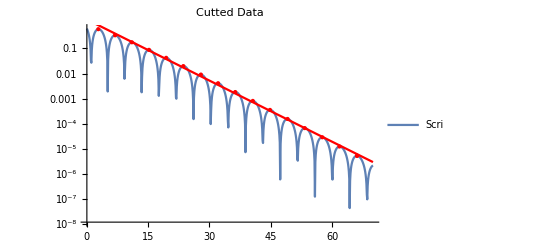

```mathematica
FitData=Table[{MaxData[[i,1]],Log@MaxData[[i,2]]},{i,1,MaxSize}];
FitExp=Fit[FitData,{1,t},t];
PlotFit=LogPlot[Exp@FitExp, {t,t0,t1}, PlotStyle->Red];
ωI=D[FitExp,t]
Show[PlotData,PlotMax, PlotFit]
```

#### Fourier Transform According to Help

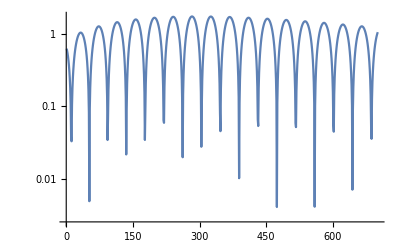

```mathematica
Period=Table[ Data[[k]]*Exp[-ωI*tData[[k]]], {k,1, NData}];
PlotPeriod=ListLogPlot[Abs@Period, PlotRange->Full, Joined->True];
Show[PlotPeriod]
```

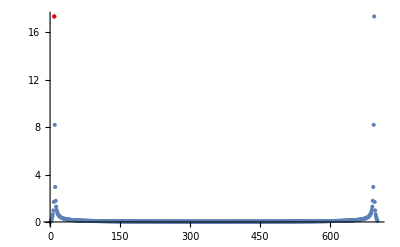

```mathematica
FourierPeriod=Abs[Fourier[Period]];

NFourier=Length@FourierPeriod;
FourierPeriod1=Table[FourierPeriod[[i]], {i,1,NFourier/2}];
FourierPeriod2=Table[FourierPeriod[[i-NFourier/2]], {i,NFourier/2+1,NFourier}];
pos = Position[FourierPeriod1, Max[FourierPeriod1]][[1,1]];


Show[ListPlot[FourierPeriod], Graphics[{Red, Point[{pos, FourierPeriod[[pos]]}]}], PlotRange->All]
```

```mathematica
fr = Abs[Fourier[Period Exp[2 Pi I (pos - 2) N[Range[0, NData - 1]]/NData], FourierParameters->{0,2/NData}]];
frpos = Position[fr, Max[fr]][[1,1]]
```

451

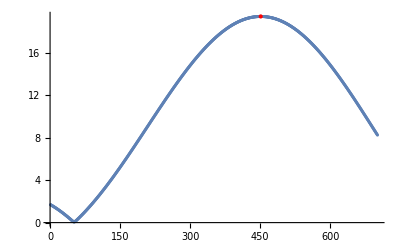

```mathematica
Show[ListPlot[fr], Graphics[{Red, Point[{frpos, fr[[frpos]]}]}], PlotRange->All]
```

```mathematica
Per=N[NData/(pos - 2 + 2 (frpos - 1)/NData)];
ωR=N[2*Pi/(Per*h)]
```

0.742499

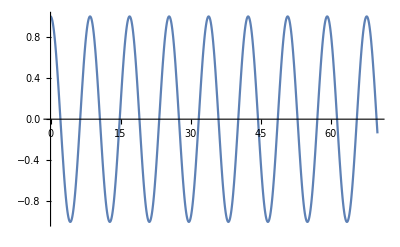

```mathematica
Plot[Cos[ωR*t], {t,t0,t1}]
```

#### Print Results

```mathematica
Print["Imaginary QNM ωI = ",ωI]
Print["Real QNM ωR  = ",ωR]
```

Imaginary QNM ωI = -0.18690669828540074

Real QNM ωR  = 0.742499

```mathematica
N[s$QNM]
```

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ}

```mathematica
s$mean=(N[s$QNM[[3]]]+Conjugate[N[s$QNM[[4]]]])/2
```

-0.21444-0.737755 ⅈ

```mathematica
sSchwarzschil$n0=-0.1779246313778724125652120005152178509675423181561187703639623721770992017316962715759234642097336789737598225764160641944325887735662226216980430348181479+I* 0.747343368836081044564012120434754107823160172903535881938910623355711335675523008900239525461539174202261286644053489464729872338914566586615874614796782;
N[sSchwarzschil$n0,3]
```

-0.18+0.747 ⅈ